```mathematica
ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{1,2},{1,3}},10,"StatesPlotsList"]
```

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}},{{0,0,0},{0,0}},20,"StatesList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}},{{0,0,0},{0,0}},10,"StatesList"]]
```

9

```mathematica
Length[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{1,2},{1,3}},20,"StatesList"]]
```

21

```mathematica
HypergraphRuleMutation[]
```

```mathematica
ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}},{{0,0,0},{0,0}},20,"StatesList"]
```

{{{0,0,0},{0,0}},{{0,0,1},{0,0},{0,0}},{{0,0},{0,0,2},{1,0},{1,0}},{{1,0},{1,0},{0,0,3},{2,0},{2,0}},{{1,0},{2,0},{2,0},{0,1,4},{3,0},{3,1}},{{2,0},{2,0},{3,0},{3,1},{0,1,5},{4,1},{4,1}},{{2,0},{3,0},{3,1},{4,1},{4,1},{0,2,6},{5,1},{5,2}},{{3,0},{3,1},{4,1},{4,1},{5,1},{5,2},{0,2,7},{6,2},{6,2}},{{3,1},{4,1},{4,1},{5,1},{5,2},{6,2},{6,2},{0,3,8},{7,2},{7,3}}}

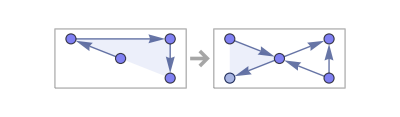

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}, {u, y}}]]
```

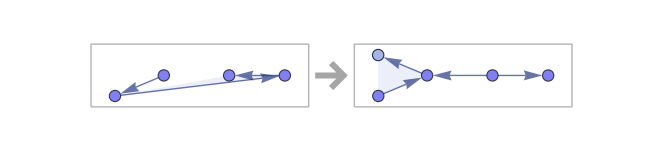

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}}]]
```

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}},{{0,0,0},{0,0}},20,"StatesList"]
```

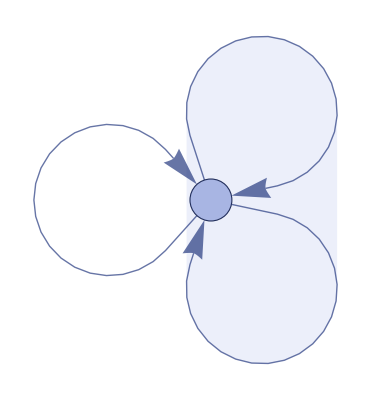
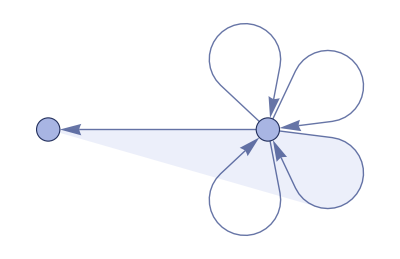
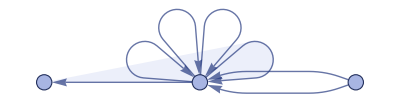
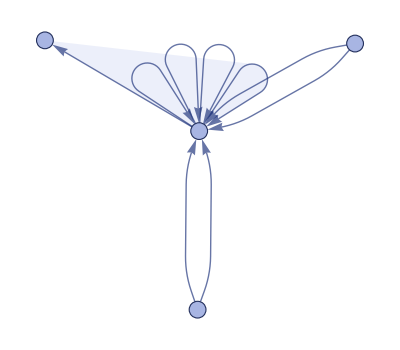
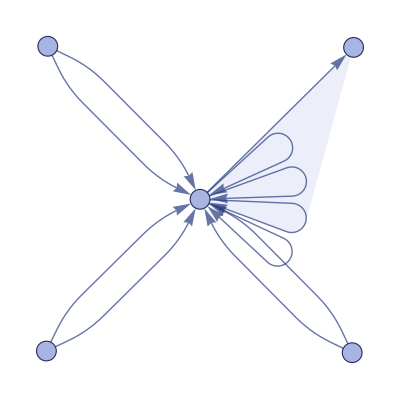
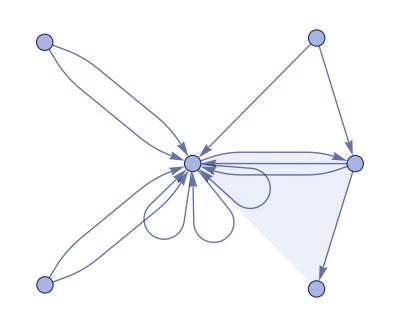
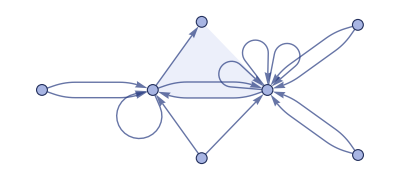
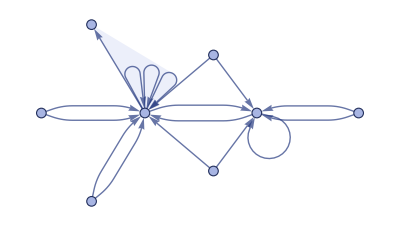

```mathematica
ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}, {u, y}}, {{0,0,0},{0,0}},40,"StatesPlotsList"]
```

#### Possible mutations:

- Edge to a new node
- Edge to an old node
- Delete an edge

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}},{{0,0,0},{0,0}},20,"StatesList"]
```

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y,z},{u,x}}->{{x,u,v},{z,y},{z,u}}]]
```

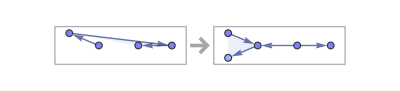

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{a, b, c},{d,a}}->{{a,d,e},{c,b},{c,d}}]]
```

```mathematica
currmaxletter = "e";
```

```mathematica
Alphabet[][[1]]
```

a

```mathematica
Head[]
```

String

```mathematica
ToExpression[]
```

a

```mathematica
Head[]
```

Symbol

```mathematica
=== b
```

False

```mathematica
{{a, b, c},{d,a}}->{{a,d,e},{c,b},{c,d}}
```

```mathematica
maxletteridx = 5;
```

```mathematica
currnodes = ToExpression/@ Take[Alphabet[], maxletteridx]
```

{a,b,c,d,e}

```mathematica
If[]
```

```mathematica
RandomHypergraphRuleMutation[rule_]:= Module[{},

]
```

```mathematica
8
```

8

```mathematica
Mod[10, 26]
```

10

```mathematica
RandomHypergraphRuleMutation[edges_]:= Module[{},
nodes = {DeleteDuplicates[Flatten[edges]], edges};
newsymbol = ToExpression[Alphabet[][[Mod[Length[nodes], 26]]]<>If[# == 0, "", ToString[#]]&[Floor[Length[nodes] /26]]];src = RandomChoice[Append[nodes, newsymbol]];
target= If[src === newsymbol, RandomChoice[nodes], RandomChoice[Append[nodes, newsymbol]]];
{If[src === newsymbol  || target === newsymbol, Append[nodes, newsymbol], nodes], Append[edges, {src, target}]}]
```

```mathematica
ClearAll[RandomHypergraphMutation];RandomHypergraphMutation[edges_]:= Module[{},
nodes = DeleteDuplicates[Flatten[edges]];
newsymbol = ToExpression[Alphabet[][[Mod[Length[nodes], 26] + 1]]<>If[# == 0, "", ToString[#]]&[Floor[Length[nodes] /26]]];src = RandomChoice[Append[nodes, newsymbol]];
target= If[src === newsymbol, RandomChoice[nodes], RandomChoice[Append[nodes, newsymbol]]];
Append[edges, {src, target}]]
```

```mathematica
{{a, b, c},{d,a}}->{{a,d,e},{c,b},{c,d}}
```

```mathematica
RandomHypergraphRuleMutation[{{a,d,e},{c,b},{c,d}}]
```

{{a,d,e},{c,b},{c,d},{e,e}}

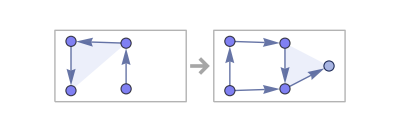
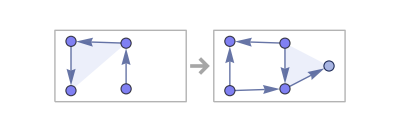
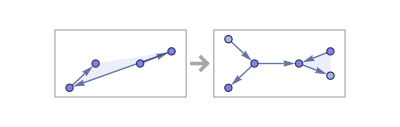
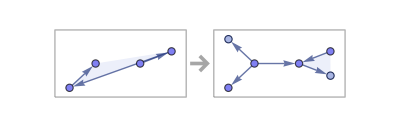
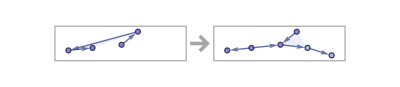
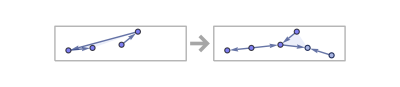
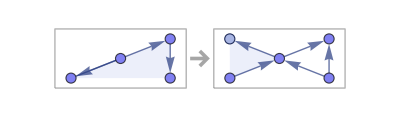
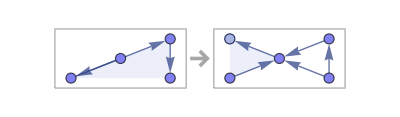

```mathematica
Union[Table[RulePlot[ResourceFunction["WolframModel"][{{a, b, c},{d,a}}->RandomHypergraphMutation[{{a,d,e},{c,b},{c,d}}]]], 200]]
```

```mathematica
Length[]
```

35

```mathematica
newsymbol
```

e

```mathematica
nodes
```

{{a,d,e,c,b},{{a,d,e},{c,b},{c,d}}}

#### Running first adaptations

```mathematica
MapAt[# + 1&, 1->2, 2]
```

1→3

```mathematica
##&@<|a->1, b->2|>
```

<|a→1,b→2|>

```mathematica
SeedRandom[333220];Module[{cut = 200}, NestList[Block[{newrule = MapAt[RandomHypergraphMutation, #Rule, 2], newfitness},
newfitness =If[# >= cut, 0,#]&[ Length[ResourceFunction["WolframModel"][newrule, {{0,0,0},{0,0}},cut,"StatesList"]]];
If[newfitness>= #Fitness, <|"Rule"->newrule, "Fitness"->newfitness|>,##]
]&, <|"Rule"->{{a, b, c},{d,a}}->{{a,d,e},{c,b},{c,d}}, "Fitness"->9|>, 100]]
```

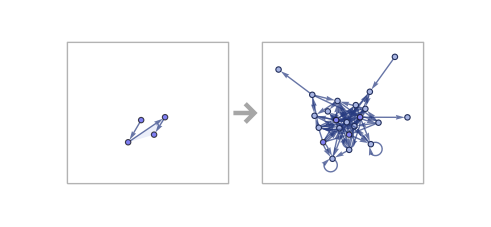

```mathematica
RulePlot[ResourceFunction["WolframModel"][[[-1, "Rule"]]]]
```

```mathematica
GatherBy[,#Fitness&][[All, 1]]
```

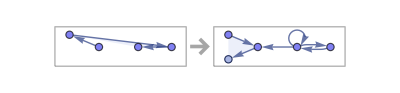
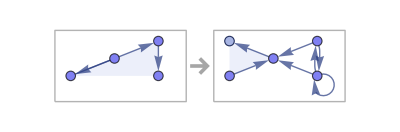
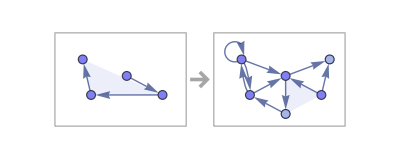
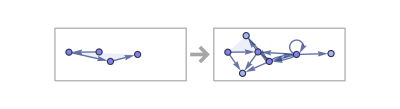
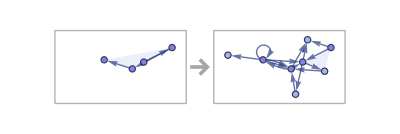
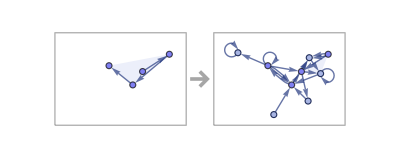
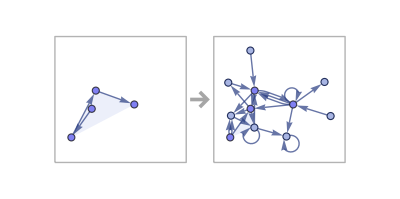
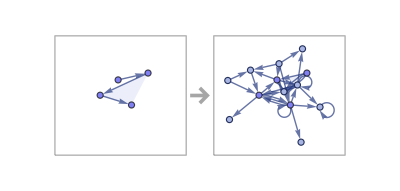
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RulePlot[ResourceFunction["WolframModel"][#Rule]]&/@ GatherBy[,#Fitness&][[All, 1]]
```

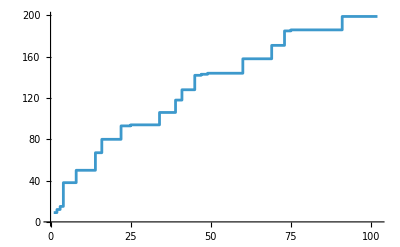

```mathematica
ListStepPlot[[[All, "Fitness"]]]
```

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][[[-1, "Rule"]], {{0,0,0},{0,0}},200,"StatesList"][[1;;All;;10]]
```

$Aborted

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][[[-1, "Rule"]], {{0,0,0},{0,0}},200,"StatesList"][[{-1}]]
```

{-Graphics-}

```mathematica
GraphPlot3D[ResourceFunction["HypergraphToGraph"][ResourceFunction["WolframModel"][[[-1, "Rule"]], {{0,0,0},{0,0}},200,"FinalState"]]]
```

-Graphics3D-

```mathematica
ResourceFunction["WolframModel"][[[-1, "Rule"]],{{0,0,0},{0,0}},200,"FinalState"]
```

{{0,0,0},{0,0,0}}

```mathematica
ResourceFunction["GraphReconstructedSurface"][ResourceFunction["WolframModel"][[[-1, "Rule"]],{{0,0,0},{0,0}},200,"FinalState"]]
```

-Graphics3D-

```mathematica
GraphPlot3D[ResourceFunction["HypergraphToGraph"][ResourceFunction["WolframModel"][{{x,x,y},{x,z,u}}->{{u,u,z},{y,v,z},{y,v,z}},{{0,0,0},{0,0,0}},500,"FinalState"]],VertexStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph3D","VertexStyle"],EdgeStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph3D","EdgeLineStyle"]]
```

```mathematica
ResourceFunction["WolframModel"][{{x,x,y},{x,z,u}}->{{u,u,z},{y,v,z},{y,v,z}},{{0,0,0},{0,0,0}},1000,"FinalStatePlot"]
```

```mathematica
Graph3D[]
```

Graph3D[{-Graphics-}]

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][[[-1, "Rule"]], {{0,0,0},{0,0}},200,"StatesList"][[{-1}]]
```

```mathematica
Length[ResourceFunction["WolframModel"][[[-1, "Rule"]], {{0,0,0},{0,0}},200,"StatesList"][[1;;All;;20]]]
```

9

```mathematica
RemoveDanglingEndsU[graph_]:=VertexDelete[graph,Pick[VertexList[graph],#<2&/@VertexOutDegree[UndirectedGraph[graph]]]]
```

```mathematica
Apply[List,EdgeList/@RemoveDanglingEndsU/@Graph/@Apply[Rule,ResourceFunction["WolframModel"][{{1,2},{2,3}}->{{4,1},{4,3},{2,1},{2,3},{4,5}},{{0,0},{0,0}},9,"StatesList"],{2}],{2}]
```

{{{0,0},{0,0}},{{1,0},{1,0},{0,0},{0,0}},{{3,1},{3,0},{0,1},{0,0},{5,1},{5,0},{0,1},{0,0}},{{5,1},{7,3},{7,2},{1,3},{1,2},{9,3},{9,1},{0,3},{0,1},{11,5},{11,0},{0,5},{0,0},{13,0},{13,1},{0,0},{0,1}},{{7,2},{9,3},{13,1},{15,7},{15,4},{3,7},{3,4},{17,5},{17,3},{1,5},{1,3},{19,9},{19,2},{1,9},{1,2},{21,11},{21,6},{5,11},{5,6},{23,11},{23,3},{0,11},{0,3},{25,0},{25,1},{0,0},{0,1},{27,13},{27,5},{0,13},{0,5},{29,0},{29,1},{0,0},{0,1}},{{15,4},{17,3},{19,2},{21,6},{23,11},{23,3},{0,1},{31,15},{31,2},{7,15},{7,2},{33,3},{33,8},{7,3},{7,8},{35,9},{35,4},{3,9},{3,4},{37,13},{37,5},{1,13},{1,5},{39,19},{39,10},{9,19},{9,10},{41,21},{41,12},{11,21},{11,12},{43,17},{43,11},{5,17},{5,11},{45,25},{45,11},{0,25},{0,11},{47,25},{47,3},{1,25},{1,3},{49,0},{49,3},{0,0},{0,3},{51,0},{51,9},{1,0},{1,9},{53,27},{53,14},{13,27},{13,14},{55,27},{55,6},{5,27},{5,6},{57,29},{57,13},{0,29},{0,13},{59,29},{59,2},{1,29},{1,2},{61,0},{61,5},{0,0},{0,5}},{{31,2},{7,2},{33,3},{33,8},{7,3},{7,8},{35,4},{39,10},{41,12},{43,11},{45,11},{47,25},{47,3},{1,25},{1,3},{49,3},{51,9},{1,9},{53,14},{55,27},{55,6},{59,29},{59,2},{1,29},{1,2},{0,0},{63,31},{63,4},{15,31},{15,4},{65,7},{65,16},{15,7},{15,16},{67,17},{67,9},{3,17},{3,9},{69,23},{69,4},{3,23},{3,4},{71,0},{71,13},{1,0},{1,13},{73,39},{73,2},{19,39},{19,2},{75,9},{75,20},{19,9},{19,20},{77,35},{77,10},{9,35},{9,10},{79,41},{79,6},{21,41},{21,6},{81,11},{81,22},{21,11},{21,22},{83,23},{83,12},{11,23},{11,12},{85,43},{85,18},{17,43},{17,18},{87,37},{87,17},{5,37},{5,17},{89,1},{89,11},{5,1},{5,11},{91,45},{91,26},{25,45},{25,26},{93,49},{93,25},{0,49},{0,25},{95,0},{95,11},{0,0},{0,11},{97,51},{97,3},{0,51},{0,3},{99,53},{99,28},{27,53},{27,28},{101,37},{101,27},{13,37},{13,27},{103,57},{103,30},{29,57},{29,30},{105,57},{105,14},{13,57},{13,14},{107,1},{107,29},{0,1},{0,29},{109,61},{109,13},{0,61},{0,13},{111,61},{111,27},{5,61},{5,27},{113,0},{113,6},{5,0},{5,6}},{{33,8},{7,8},{55,6},{59,2},{63,4},{15,4},{65,16},{15,16},{67,9},{69,4},{73,2},{19,2},{75,9},{75,20},{19,9},{19,20},{77,10},{79,6},{21,6},{81,11},{81,22},{21,11},{21,22},{83,23},{83,12},{85,18},{5,37},{5,17},{89,11},{5,11},{91,26},{95,11},{97,3},{99,28},{101,37},{101,27},{103,30},{105,57},{105,14},{107,29},{0,1},{0,29},{0,61},{111,61},{111,27},{5,61},{5,27},{113,6},{5,6},{115,63},{115,2},{31,63},{31,2},{117,15},{117,32},{31,15},{31,32},{119,65},{119,2},{7,65},{7,2},{121,15},{121,3},{7,15},{7,3},{123,33},{123,17},{3,33},{3,17},{125,47},{125,9},{3,47},{3,9},{127,69},{127,24},{23,69},{23,24},{129,1},{129,23},{3,1},{3,23},{131,49},{131,4},{3,49},{3,4},{133,71},{133,0},{0,71},{0,0},{135,73},{135,10},{39,73},{39,10},{137,19},{137,40},{39,19},{39,40},{139,77},{139,4},{35,77},{35,4},{141,9},{141,36},{35,9},{35,36},{143,51},{143,10},{9,51},{9,10},{145,79},{145,12},{41,79},{41,12},{147,21},{147,42},{41,21},{41,42},{149,43},{149,23},{11,43},{11,23},{151,45},{151,12},{11,45},{11,12},{153,85},{153,44},{43,85},{43,44},{155,67},{155,43},{17,67},{17,43},{157,87},{157,38},{37,87},{37,38},{159,87},{159,18},{17,87},{17,18},{161,89},{161,25},{1,89},{1,25},{163,5},{163,9},{1,5},{1,9},{165,91},{165,46},{45,91},{45,46},{167,47},{167,45},{25,47},{25,45},{169,93},{169,50},{49,93},{49,50},{171,93},{171,26},{25,93},{25,26},{173,1},{173,49},{0,1},{0,49},{175,95},{175,25},{0,95},{0,25},{177,0},{177,11},{0,0},{0,11},{179,97},{179,52},{51,97},{51,52},{181,99},{181,14},{53,99},{53,14},{183,27},{183,54},{53,27},{53,54},{185,55},{185,28},{27,55},{27,28},{187,71},{187,37},{13,71},{13,37},{189,1},{189,27},{13,1},{13,27},{191,103},{191,58},{57,103},{57,58},{193,59},{193,57},{29,59},{29,57},{195,1},{195,30},{29,1},{29,30},{197,107},{197,2},{1,107},{1,2},{199,109},{199,62},{61,109},{61,62},{201,109},{201,57},{13,109},{13,57},{203,0},{203,14},{13,0},{13,14},{205,113},{205,51},{0,113},{0,51},{207,5},{207,3},{0,5},{0,3}},{{7,8},{75,20},{19,20},{81,22},{21,22},{83,12},{105,14},{111,27},{115,2},{31,2},{117,32},{31,32},{119,2},{7,2},{121,15},{7,15},{125,9},{127,24},{129,23},{131,4},{135,10},{39,10},{137,40},{39,40},{139,4},{35,4},{141,9},{141,36},{35,9},{35,36},{143,10},{145,12},{41,12},{147,42},{41,42},{149,23},{151,12},{153,44},{155,43},{157,38},{159,87},{159,18},{17,87},{17,18},{163,9},{165,46},{167,47},{167,45},{169,50},{171,93},{171,26},{25,26},{173,49},{177,11},{0,11},{179,52},{181,14},{53,14},{183,27},{183,54},{53,27},{53,54},{185,28},{187,71},{187,37},{13,71},{13,37},{189,27},{13,1},{13,27},{191,58},{193,57},{195,1},{195,30},{29,1},{29,30},{197,2},{199,62},{61,62},{201,109},{201,57},{13,109},{13,57},{203,14},{13,14},{0,51},{0,5},{209,115},{209,4},{63,115},{63,4},{211,31},{211,64},{63,31},{63,64},{213,117},{213,4},{15,117},{15,4},{215,31},{215,16},{15,31},{15,16},{217,119},{217,16},{65,119},{65,16},{219,7},{219,66},{65,7},{65,66},{221,123},{221,8},{33,123},{33,8},{223,3},{223,34},{33,3},{33,34},{225,97},{225,17},{3,97},{3,17},{227,125},{227,48},{47,125},{47,48},{229,121},{229,47},{3,121},{3,47},{231,7},{231,9},{3,7},{3,9},{233,127},{233,4},{69,127},{69,4},{235,23},{235,70},{69,23},{69,70},{237,83},{237,24},{23,83},{23,24},{239,133},{239,72},{71,133},{71,72},{241,133},{241,1},{0,133},{0,1},{243,0},{243,29},{0,0},{0,29},{245,135},{245,2},{73,135},{73,2},{247,39},{247,74},{73,39},{73,74},{249,137},{249,2},{19,137},{19,2},{251,39},{251,9},{19,39},{19,9},{253,139},{253,10},{77,139},{77,10},{255,35},{255,78},{77,35},{77,78},{257,67},{257,51},{9,67},{9,51},{259,75},{259,10},{9,75},{9,10},{261,145},{261,6},{79,145},{79,6},{263,41},{263,80},{79,41},{79,80},{265,147},{265,6},{21,147},{21,6},{267,41},{267,11},{21,41},{21,11},{269,81},{269,43},{11,81},{11,43},{271,89},{271,23},{11,89},{11,23},{273,5},{273,45},{11,5},{11,45},{275,95},{275,12},{11,95},{11,12},{277,153},{277,18},{85,153},{85,18},{279,43},{279,86},{85,43},{85,86},{281,149},{281,44},{43,149},{43,44},{283,155},{283,68},{67,155},{67,68},{285,5},{285,67},{17,5},{17,67},{287,123},{287,43},{17,123},{17,43},{289,157},{289,88},{87,157},{87,88},{291,5},{291,87},{37,5},{37,87},{293,101},{293,38},{37,101},{37,38},{295,161},{295,90},{89,161},{89,90},{297,129},{297,89},{1,129},{1,89},{299,3},{299,25},{1,3},{1,25},{301,163},{301,61},{5,163},{5,61},{303,1},{303,27},{5,1},{5,27},{305,165},{305,26},{91,165},{91,26},{307,45},{307,92},{91,45},{91,92},{309,151},{309,46},{45,151},{45,46},{311,161},{311,47},{25,161},{25,47},{313,169},{313,94},{93,169},{93,94},{315,131},{315,93},{49,131},{49,93},{317,3},{317,50},{49,3},{49,50},{319,173},{319,9},{1,173},{1,9},{321,175},{321,96},{95,175},{95,96},{323,175},{323,45},{25,175},{25,45},{325,0},{325,93},{25,0},{25,93},{327,177},{327,61},{0,177},{0,61},{329,0},{329,71},{0,0},{0,71},{331,179},{331,98},{97,179},{97,98},{333,143},{333,97},{51,143},{51,97},{335,181},{335,28},{99,181},{99,28},{337,53},{337,100},{99,53},{99,100},{339,185},{339,6},{55,185},{55,6},{341,27},{341,56},{55,27},{55,56},{343,101},{343,28},{27,101},{27,28},{345,191},{345,30},{103,191},{103,30},{347,57},{347,104},{103,57},{103,104},{349,105},{349,58},{57,105},{57,58},{351,193},{351,2},{59,193},{59,2},{353,29},{353,60},{59,29},{59,60},{355,107},{355,57},{29,107},{29,57},{357,197},{357,108},{107,197},{107,108},{359,0},{359,107},{1,0},{1,107},{361,189},{361,2},{1,189},{1,2},{363,199},{363,110},{109,199},{109,110},{365,111},{365,109},{61,111},{61,109},{367,203},{367,49},{0,203},{0,49},{369,13},{369,95},{0,13},{0,95},{371,205},{371,6},{113,205},{113,6},{373,205},{373,52},{51,205},{51,52},{375,0},{375,114},{113,0},{113,114},{377,207},{377,6},{5,207},{5,6},{379,207},{379,23},{3,207},{3,23},{381,0},{381,4},{3,0},{3,4}},{{19,20},{21,22},{141,36},{35,36},{159,18},{171,26},{183,54},{53,54},{195,30},{201,57},{13,57},{13,14},{209,4},{63,4},{211,64},{63,64},{213,4},{215,31},{215,16},{15,16},{217,16},{65,16},{219,66},{65,66},{221,8},{33,123},{33,8},{223,34},{33,34},{227,48},{229,47},{231,7},{233,4},{69,4},{235,23},{235,70},{69,23},{69,70},{237,24},{239,72},{241,133},{245,2},{73,2},{247,74},{73,74},{249,2},{19,2},{251,39},{251,9},{19,39},{19,9},{253,10},{77,10},{255,78},{77,78},{259,10},{261,6},{79,6},{263,80},{79,80},{265,6},{21,6},{267,41},{21,41},{269,43},{271,23},{273,45},{11,45},{275,12},{11,12},{277,18},{85,18},{279,43},{279,86},{85,43},{85,86},{281,44},{283,68},{17,67},{287,123},{287,43},{17,123},{17,43},{289,88},{291,87},{293,38},{37,101},{37,38},{295,90},{303,27},{305,26},{91,26},{307,45},{307,92},{91,45},{91,92},{309,46},{311,161},{311,47},{25,161},{25,47},{313,94},{315,93},{317,50},{319,9},{321,96},{323,175},{323,45},{25,175},{25,45},{325,93},{25,93},{329,71},{331,98},{333,97},{335,28},{99,28},{337,100},{99,100},{339,6},{55,6},{341,27},{341,56},{55,27},{55,56},{343,101},{343,28},{345,30},{103,30},{347,57},{347,104},{103,57},{103,104},{349,58},{351,2},{59,193},{59,2},{353,60},{59,60},{355,57},{357,108},{359,107},{1,0},{1,107},{361,2},{1,2},{363,110},{365,109},{61,109},{369,95},{371,6},{113,205},{113,6},{373,205},{373,52},{51,205},{51,52},{375,0},{375,114},{113,0},{113,114},{377,6},{379,207},{379,23},{3,207},{3,23},{381,0},{381,4},{3,0},{3,4},{383,209},{383,2},{115,209},{115,2},{385,63},{385,116},{115,63},{115,116},{387,211},{387,2},{31,211},{31,2},{389,63},{389,32},{31,63},{31,32},{391,213},{391,32},{117,213},{117,32},{393,15},{393,118},{117,15},{117,118},{395,121},{395,4},{15,121},{15,4},{397,7},{397,31},{15,7},{15,31},{399,217},{399,2},{119,217},{119,2},{401,65},{401,120},{119,65},{119,120},{403,219},{403,8},{7,219},{7,8},{405,65},{405,2},{7,65},{7,2},{407,221},{407,124},{123,221},{123,124},{409,225},{409,87},{17,225},{17,87},{411,223},{411,97},{3,223},{3,97},{413,3},{413,18},{17,3},{17,18},{415,227},{415,9},{125,227},{125,9},{417,47},{417,126},{125,47},{125,126},{419,167},{419,48},{47,167},{47,48},{421,229},{421,122},{121,229},{121,122},{423,33},{423,121},{3,33},{3,121},{425,233},{425,24},{127,233},{127,24},{427,69},{427,128},{127,69},{127,128},{429,237},{429,12},{83,237},{83,12},{431,23},{431,84},{83,23},{83,84},{433,129},{433,24},{23,129},{23,24},{435,239},{435,134},{133,239},{133,134},{437,187},{437,133},{71,187},{71,133},{439,13},{439,72},{71,13},{71,72},{441,243},{441,11},{0,243},{0,11},{443,243},{443,1},{29,243},{29,1},{445,0},{445,51},{0,0},{0,51},{447,0},{447,30},{29,0},{29,30},{449,245},{449,10},{135,245},{135,10},{451,73},{451,136},{135,73},{135,136},{453,247},{453,10},{39,247},{39,10},{455,73},{455,40},{39,73},{39,40},{457,249},{457,40},{137,249},{137,40},{459,19},{459,138},{137,19},{137,138},{461,253},{461,4},{139,253},{139,4},{463,77},{463,140},{139,77},{139,140},{465,255},{465,4},{35,255},{35,4},{467,77},{467,9},{35,77},{35,9},{469,141},{469,67},{9,141},{9,67},{471,163},{471,51},{9,163},{9,51},{473,259},{473,20},{75,259},{75,20},{475,9},{475,76},{75,9},{75,76},{477,231},{477,10},{9,231},{9,10},{479,261},{479,12},{145,261},{145,12},{481,79},{481,146},{145,79},{145,146},{483,263},{483,12},{41,263},{41,12},{485,79},{485,42},{41,79},{41,42},{487,265},{487,42},{147,265},{147,42},{489,21},{489,148},{147,21},{147,148},{491,269},{491,22},{81,269},{81,22},{493,11},{493,82},{81,11},{81,82},{495,177},{495,43},{11,177},{11,43},{497,267},{497,89},{11,267},{11,89},{499,21},{499,23},{11,21},{11,23},{501,277},{501,44},{153,277},{153,44},{503,85},{503,154},{153,85},{153,154},{505,281},{505,23},{149,281},{149,23},{507,43},{507,150},{149,43},{149,150},{509,155},{509,44},{43,155},{43,44},{511,283},{511,156},{155,283},{155,156},{513,257},{513,155},{67,257},{67,155},{515,285},{515,68},{67,285},{67,68},{517,289},{517,38},{157,289},{157,38},{519,87},{519,158},{157,87},{157,158},{521,159},{521,88},{87,159},{87,88},{523,187},{523,5},{37,187},{37,5},{525,13},{525,87},{37,13},{37,87},{527,293},{527,102},{101,293},{101,102},{529,295},{529,162},{161,295},{161,162},{531,271},{531,161},{89,271},{89,161},{533,297},{533,130},{129,297},{129,130},{535,297},{535,90},{89,297},{89,90},{537,13},{537,129},{1,13},{1,129},{539,195},{539,89},{1,195},{1,89},{541,299},{541,47},{3,299},{3,47},{543,299},{543,26},{25,299},{25,26},{545,1},{545,7},{3,1},{3,7},{547,241},{547,25},{1,241},{1,25},{549,301},{549,164},{163,301},{163,164},{551,301},{551,62},{61,301},{61,62},{553,0},{553,163},{5,0},{5,163},{555,273},{555,61},{5,273},{5,61},{557,11},{557,1},{5,11},{5,1},{559,285},{559,27},{5,285},{5,27},{561,305},{561,46},{165,305},{165,46},{563,91},{563,166},{165,91},{165,166},{565,309},{565,12},{151,309},{151,12},{567,45},{567,152},{151,45},{151,152},{569,167},{569,46},{45,167},{45,46},{571,313},{571,50},{169,313},{169,50},{573,93},{573,170},{169,93},{169,170},{575,171},{575,94},{93,171},{93,94},{577,315},{577,4},{131,315},{131,4},{579,49},{579,132},{131,49},{131,132},{581,173},{581,93},{49,173},{49,93},{583,317},{583,9},{3,317},{3,9},{585,319},{585,174},{173,319},{173,174},{587,0},{587,173},{1,0},{1,173},{589,303},{589,9},{1,303},{1,9},{591,321},{591,176},{175,321},{175,176},{593,275},{593,175},{95,275},{95,175},{595,11},{595,96},{95,11},{95,96},{597,325},{597,133},{0,325},{0,133},{599,327},{599,178},{177,327},{177,178},{601,25},{601,177},{0,25},{0,177},{603,329},{603,61},{0,329},{0,61},{605,0},{605,71},{0,0},{0,71},{607,331},{607,52},{179,331},{179,52},{609,97},{609,180},{179,97},{179,180},{611,225},{611,98},{97,225},{97,98},{613,333},{613,10},{143,333},{143,10},{615,51},{615,144},{143,51},{143,144},{617,257},{617,97},{51,257},{51,97},{619,335},{619,14},{181,335},{181,14},{621,99},{621,182},{181,99},{181,182},{623,337},{623,14},{53,337},{53,14},{625,99},{625,27},{53,99},{53,27},{627,339},{627,28},{185,339},{185,28},{629,55},{629,186},{185,55},{185,186},{631,111},{631,101},{27,111},{27,101},{633,183},{633,28},{27,183},{27,28},{635,345},{635,58},{191,345},{191,58},{637,103},{637,192},{191,103},{191,192},{639,349},{639,14},{105,349},{105,14},{641,57},{641,106},{105,57},{105,106},{643,193},{643,58},{57,193},{57,58},{645,351},{645,194},{193,351},{193,194},{647,353},{647,107},{29,353},{29,107},{649,59},{649,57},{29,59},{29,57},{651,357},{651,2},{197,357},{197,2},{653,107},{653,198},{197,107},{197,198},{655,355},{655,108},{107,355},{107,108},{657,361},{657,27},{189,361},{189,27},{659,1},{659,190},{189,1},{189,190},{661,363},{661,62},{199,363},{199,62},{663,109},{663,200},{199,109},{199,200},{665,201},{665,110},{109,201},{109,110},{667,365},{667,112},{111,365},{111,112},{669,327},{669,111},{61,327},{61,111},{671,367},{671,14},{203,367},{203,14},{673,367},{673,3},{49,367},{49,3},{675,0},{675,204},{203,0},{203,204},{677,0},{677,50},{49,0},{49,50},{679,369},{679,27},{13,369},{13,27},{681,0},{681,109},{13,0},{13,109},{683,359},{683,95},{0,359},{0,95},{685,371},{685,206},{205,371},{205,206},{687,377},{687,208},{207,377},{207,208},{689,17},{689,207},{5,17},{5,207},{691,291},{691,6},{5,291},{5,6}}}

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@Apply[List,EdgeList/@RemoveDanglingEndsU/@Graph/@Apply[Rule,ResourceFunction["WolframModel"][{{1,2},{2,3}}->{{4,1},{4,3},{2,1},{2,3},{4,5}},{{0,0},{0,0}},9,"StatesList"],{2}],{2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Allowing one to delete edges

#### Trying starting with multiple rules and limiting complexity